```mathematica
A1=Plot3D[400 - (2*(x^2) - (3* (y^2))),{x,-12,12},{y,-12,12},PlotStyle->Directive[Brown,Specularity[White,20],Opacity[0.8]]];
```

```mathematica
A2=Graphics3D[{Blue,PointSize[0.05],Point[{1,2,386}]}];
```

```mathematica
A3= Graphics3D[{Black,Thick,Arrow[{{0,-10,3970},{1,2,400}}]}];
```

```mathematica
A4= Graphics3D[{Green,Thick,Dashed,Line[{{0,-1,426},{1,2,386}}]}];
A5= Graphics3D[{Red,Thick,Arrow[{{1,2,386},{1-(10/Sqrt[10]),2-(30/Sqrt[10]),386+(400/Sqrt[10])}}]}];
```

```mathematica
Show[A1,A2,A3,A4,A5]
```

-Graphics3D-

```mathematica
A6=ContourPlot[400 - (2*(x^2) - (3* (y^2))),{x,-12,12},{y,-12,12},PlotLegends->Automatic];
```

```mathematica
A7=Graphics[{Blue,PointSize[0.05],Point[{1,2}]}];
```

```mathematica
A8= Graphics[{Red,Thick,Arrow[{{0,0},{-4,-12}}]}];
```

```mathematica
A9= Graphics[{Green,Dashed,Thick,Line[{{4,12},{-4,-12}}]}];
```

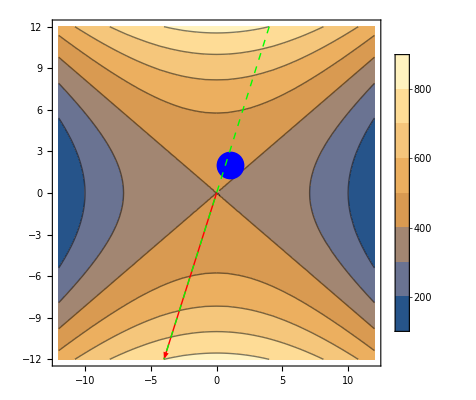

```mathematica
Show[A6,A7,A8,A9]
```